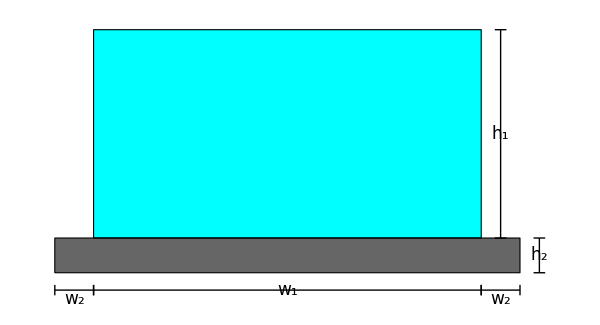

```mathematica
Module[{w1,h1,w2,h2,δ0,δ1,δ3},
w1=5;h1=3;w2=0.5;h2=0.5;
δ0=0.75;δ1=0.75;δ3=0.25;

Graphics[{EdgeForm@Thick,
{FaceForm@Cyan,Rectangle[{0,h2},{w1,h1+h2}]},
{FaceForm@GrayLevel@0.4,Rectangle[{-w2,0},{w1+w2,h2}]},

(*MEASUREMENTS*)
Line[{{0,h2-δ0},{w1,h2-δ0}}],Line[{{#,h2-1.1*δ0},{#,h2-0.9*δ0}}]&/@{0,w1},
Text[Style[Subscript[Style["w",Italic],1],17,Background->White],{0.5*w1,h2-δ0}],

Line[{{-w2,h2-δ1},{0,h2-δ1}}],Line[{{w1,h2-δ1},{w1+w2,h2-δ1}}],Line[{{#,h2-1.1*δ1},{#,h2-0.9*δ1}}]&/@{-w2,0,w1,w1+w2},
Text[Style[Subscript[Style["w",Italic],2],17,Background->White],{#,h2-δ1},{0,1}]&/@{-0.5*w2,w1+0.5*w2},

Line[{{w1+w2+δ3,0},{w1+w2+δ3,h2}}],Line[{{w1+w2+0.7*δ3,#},{w1+w2+1.3*δ3,#}}]&/@{0,h2},
Text[Style[Subscript[Style["h",Italic],2],17,Background->White],{w1+w2+δ3,0.5*h2}],

Line[{{w1+δ3,w2},{w1+δ3,h1+h2}}],Line[{{w1+0.7*δ3,#},{w1+1.3*δ3,#}}]&/@{h2,h1+h2},
Text[Style[Subscript[Style["h",Italic],1],17,Background->White],{w1+δ3,h2+0.5*h1}]
},ImageSize->{600,325}]
]
```